```mathematica
Needs["madtomma`madinput`madinput`"]
```

Version 2.21 of Madtomma`Mfs`Mfs` loaded.  Note function name changes since Version 1.x:
interpretDescriptors→mfsInterpretKeys
keyValue→mfsKeyValue
columnNames→mfsColumnNames
descriptorNames→mfsKeyNames
colValue→mfsColumnValue
addDescriptor→mfsAddKey
editDescriptor→mfsEditKey
deleteDescriptor→mfsDeleteKey
symplecticJ→SymplecticJ

General::obspkg: "PlotLegends`" is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

Global`Thin::shdw: Symbol "Thin" appears in multiple contexts {"Global`", "System`"}; definitions in context "Global`" may shadow or be shadowed by other definitions.

Global`Delayed::shdw: Symbol "Delayed" appears in multiple contexts {"Global`", "System`"}; definitions in context "Global`" may shadow or be shadowed by other definitions.

SetDelayed::write: Tag FindPeaks in FindPeaks[data1_, data2_, Opts___] is Protected.

Needs::nocont: Context "madtomma`madinput`madinput`" was not created when Needs was evaluated.

```mathematica
Needs["gdfBinaryInterpret`"]
```

```mathematica
Needs["sddsBinaryInterpret`"]
```

```mathematica
gdfBinaryInterpret["injector_750mhz_10000.gdf",gdfVerbose->True]
```

Variables (Re)Assigned: {Bx, By, Bz, G, ID, m, nmacro, q, rmacro, rxy, t, x, y, z}

Parameters (Re)Assigned: {}

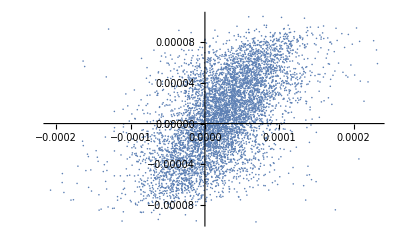

```mathematica
ListPlot[{Transpose[{y[[1]],By[[1]]/Bz[[1]]}]}]
```

```mathematica
headertext="SDDS1
!This file was created by gdf2sdds
&column name=x, units=m, type=double,  &end
&column name=y, units=m, type=double,  &end
&column name=t, units=s, type=double,  &end
&column name=xp, symbol=x', type=double,  &end
&column name=yp, symbol=y', type=double,  &end
&column name=p, units=\"m$be$nc\", type=double,  &end
&data mode=ascii &end
";
```

```mathematica
c=QuantityMagnitude[UnitConvert[Quantity["SpeedOfLight"]]];
me=QuantityMagnitude[UnitConvert[Quantity["ElectronMass"]]];
MeV=QuantityMagnitude[UnitConvert[Quantity["MeV"]]];
```

```mathematica
γ=1/(√(1-Bz^2));
```

```mathematica
v=Bz c;
```

```mathematica
p=(γ v)/c;
```

```mathematica
file=OpenWrite["injector_750mhz_10000.sdds.ascii"];
WriteString[file,headertext<>ToString[Length[p[[1]]]]<>"\n"]
Map[WriteString[file,StringJoin@@MapIndexed[If[#2[[1]]>1," ",""]<>ToString[NumberRight[#]]&,#]<>"\n"]&,Transpose[{x[[1]],y[[1]],(-z[[1]])/v[[1]],Bx[[1]]/Bz[[1]],By[[1]]/Bz[[1]],p[[1]]}]][[1]]
Close[file];
ReadList["!sddsconvert injector_750mhz_10000.sdds.ascii injector_750MHz_10000.sdds -binary"]
```

{}

```mathematica
Clear[GDF2SDDS];
GDF2SDDS[gdffile_,sddsfile_,postfix_:"",range_:All]:=Block[{c,me,MeV,MeVc,gamma,v,p,E0},
headertext="SDDS1
!This file was created by gdf2sdds
&column name=x, units=m, type=double,  &end
&column name=y, units=m, type=double,  &end
&column name=t, units=s, type=double,  &end
&column name=xp, symbol=x', type=double,  &end
&column name=yp, symbol=y', type=double,  &end
&column name=p, units=\"m$be$nc\", type=double,  &end
&data mode=ascii &end
";
Clear[Evaluate["G"<>postfix]];
gdfBinaryInterpret[gdffile,gdfVerbose->True];
c=QuantityMagnitude[UnitConvert[Quantity["SpeedOfLight"]]];
me=QuantityMagnitude[UnitConvert[Quantity["ElectronMass"]]];
MeV=QuantityMagnitude[UnitConvert[Quantity["MeV"]]];
MeVc=QuantityMagnitude[UnitConvert[Quantity["ElectronMass"]Quantity["SpeedOfLight"],"MeV/c"]];
E0=me c^2;
If[ListQ[ToExpression["G"<>postfix]],
gamma=1/(√(1-ToExpression["Bz"<>postfix]^2));,
gamma=1/(√(1-ToExpression["Bz"<>postfix]^2));
];
v=ToExpression["Bz"<>postfix] c;
p=(E0 √(-1+gamma^2))/(MeV MeVc);
file=OpenWrite[sddsfile<>".ascii"];
WriteString[file,headertext];
Block[{data=#},If[Length[#[[1]]]>0,
sddsP=#[[-1]];
WriteString[file,ToString[Length[#[[1]]]]<>"\n"];
Map[WriteString[file,StringJoin@@MapIndexed[If[#2[[1]]>1," ",""]<>ToString[NumberForm[#,32,NumberFormat->(Row[{#1,"E",#3}]&),ExponentFunction->(3 Quotient[#,3]&)]]&,#]<>"\n"]&,Transpose[data]];
]
]&/@Which[postfix=="t",Sort[Transpose[{ToExpression["x"<>postfix],ToExpression["y"<>postfix],-(#-Mean[#]&/@ToExpression["z"<>postfix])/v,ArcTan[ToExpression["Bx"<>postfix]/ToExpression["Bz"<>postfix]],ArcTan[ToExpression["By"<>postfix]/ToExpression["Bz"<>postfix]],p,ToExpression["z"<>postfix]}],Mean[#1[[-1]]]<Mean[#2[[-1]]]&][[range,1;;6]],
postfix=="p",
Print["p"];
Sort[Select[Transpose[{ToExpression["x"<>postfix],ToExpression["y"<>postfix],(#-Mean[#]&/@ToExpression["t"<>postfix]),ArcTan[ToExpression["Bx"<>postfix]/ToExpression["Bz"<>postfix]],ArcTan[ToExpression["By"<>postfix]/ToExpression["Bz"<>postfix]],p,ToExpression["t"<>postfix]}],Length[#[[-1]]]>0&],Mean[#1[[-1]]]<Mean[#2[[-1]]]&][[range,1;;6]],
postfix=="time",
Sort[Transpose[{ToExpression["x"<>postfix],ToExpression["y"<>postfix],-(#-Mean[#]&/@ToExpression["z"<>postfix])/v,ArcTan[ToExpression["Bx"<>postfix]/ToExpression["Bz"<>postfix]],ArcTan[ToExpression["By"<>postfix]/ToExpression["Bz"<>postfix]],p,ToExpression["z"<>postfix]}],Mean[#1[[-1]]]<Mean[#2[[-1]]]&][[range,1;;6]],
postfix=="position",
If[ListQ[ToExpression["G"]],
gamma=ToExpression["G"];,
gamma=1/(√(1-ToExpression["Bz"]^2));
];
v=ToExpression["Bz"] c;
p=(E0 √(-1+gamma^2))/(MeV MeVc);
Sort[Transpose[{ToExpression["x"],ToExpression["y"],-(#-Mean[#]&/@ToExpression["t"]),ToExpression["Bx"]/ToExpression["Bz"],ToExpression["By"]/ToExpression["Bz"],p,ToExpression["z"]}],Mean[#1[[-1]]]<Mean[#2[[-1]]]&][[range,1;;6]],
postfix=="",
Sort[Transpose[{ToExpression["x"<>postfix],ToExpression["y"<>postfix],-(#-Mean[#]&/@ToExpression["z"<>postfix])/v,ArcTan[ToExpression["Bx"<>postfix]/ToExpression["Bz"<>postfix]],ArcTan[ToExpression["By"<>postfix]/ToExpression["Bz"<>postfix]],p,ToExpression["z"<>postfix]}],Mean[#1[[-1]]]<Mean[#2[[-1]]]&][[range,1;;6]]];
Close[file];
ReadList["!sddsconvert "<>sddsfile<>".ascii "<>sddsfile<>" -binary"];
(*DeleteFile[sddsfile<>".ascii"]*);
]
```

```mathematica
Clear[SDDS2GDF];
SDDS2GDF[sddsfile_,gdffile_,postfix_:"",range_:All,asci2gdfPath_:""]:=Block[{c,me,MeV,gamma,v,p,MeVc,betaz,betay,betax,z,sdds2gdfz,beta},
headertext="x y z Bx By Bz G
";
sddsBinaryInterpret[sddsfile,gdfVerbose->False,sddsPrefix->"sdds2gdf"];
c=QuantityMagnitude[UnitConvert[Quantity["SpeedOfLight"]]];
me=QuantityMagnitude[UnitConvert[Quantity["ElectronMass"]]];
MeV=QuantityMagnitude[UnitConvert[Quantity["MeV"]]];
MeVc=QuantityMagnitude[UnitConvert[Quantity["ElectronMass"]Quantity["SpeedOfLight"],"MeV/c"]];
E0=me c^2;
gamma=√(1+((sdds2gdfp MeVc)/(E0/MeV))^2);
beta=√(1-gamma^-2);
betax=Tan[sdds2gdfxp] beta;
betay=Tan[sdds2gdfyp] beta;
betaz=√(beta^2-betax^2-betay^2);
sdds2gdfz=-betaz  c (sdds2gdft-Mean[sdds2gdft]);
file=OpenWrite[gdffile<>".ascii"];
WriteString[file,headertext];
If[Length[Dimensions[sdds2gdfx]]>1,
Block[{data=#},If[Length[#[[1]]]>0,
Map[WriteString[file,StringJoin@@MapIndexed[If[#2[[1]]>1," ",""]<>ToString[NumberForm[#,32,NumberFormat->(Row[{#1,"E",#3}]&),ExponentFunction->(3 Quotient[#,3]&)]]&,#]<>"\n"]&,Transpose[data]];
]
]&/@Transpose[{sdds2gdfx,sdds2gdfy,sdds2gdfz,betax,betay,betaz,gamma}],
Map[WriteString[file,StringJoin@@MapIndexed[If[#2[[1]]>1," ",""]<>ToString[NumberRight[#]]&,#]<>"\n"]&,Transpose[{sdds2gdfx,sdds2gdfy,sdds2gdfz,betax,betay,betaz,gamma}]]
];
Close[file];
ReadList["!"<>asci2gdfPath<>"asci2gdf -o "<>gdffile<>" "<>gdffile<>".ascii"];
(*DeleteFile[sddsfile<>".ascii"]*);
]
```

```mathematica
ReadList["!asci2gdf -o "<>"injector_750MHz_10000.gdf"<>" "<>"injector_750MHz_10000.gdf"<>".ascii",Record]
```

{}

```mathematica
GDF2SDDS["injector_750mhz_10000.gdf","injector_750mhz_10000.sdds","position"]
```

```mathematica
SDDS2GDF["injector_750MHz_10000.sdds","injector_750MHz_10000.sdds.gdf"]
```

```mathematica
Length[Dimensions[sdds2gdfx]]
```

1

```mathematica
sddsBinaryInterpret["injector_750mhz_10000.sdds"]
```

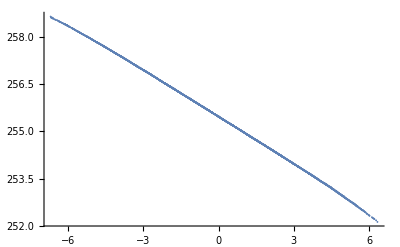

```mathematica
ListPlot[{Transpose[{10^12 t,p}]}]
```

```mathematica
GDF2SDDS["injector_750mhz_10000.gdf","injector_750mhz_10000.sdds","position"]
```

```mathematica
SDDS2GDF["injector_750mhz_10000.sdds","injector_750mhz_10000.sdds.gdf",""]
```

```mathematica
gdfBinaryInterpret["injector_750mhz_10000.gdf"]
```

```mathematica
gdfBinaryInterpret["injector_750mhz_10000.sdds.gdf",gdfPrefix->"sdds"]
```

```mathematica
sddsBz===Bz
```

False

```mathematica
sddsBx===Bx
```

False

```mathematica
Max[Abs[Chop[sddsBz-Bz]]]
```

4.90111×10^-8

```mathematica
Max[Abs[Chop[sddsBx-Bx]]]
```

0

```mathematica
Max[Abs[Chop[sddsBy-By]]]
```

0

```mathematica
Max[Abs[Chop[sddsx-x]]]
```

0

```mathematica
Max[Abs[Chop[sddsy-y]]]
```

0

```mathematica
Max[Abs[Chop[sddsz-z]]]
```

4.9871

```mathematica
SDDS2GDF["test.bun","test.bun.gdf"]
```

```mathematica
GDF2SDDS["test.bun.gdf","test.bun.sdds",""]
```

```mathematica
sddsBinaryInterpret["test.bun",sddsVerbose->True]
```

Number of Pages: 1

Variables (Re)Assigned: {x, xp, y, yp, t, p, particleID}

Parameters (Re)Assigned: {Step, pCentral, Charge, Particles, IDSlotsPerBunch}

```mathematica
sddsBinaryInterpret["test.bun.sdds",sddsPrefix->"gdf",sddsVerbose->True]
```

Number of Pages: 1

Variables (Re)Assigned: {gdfx, gdfy, gdft, gdfxp, gdfyp, gdfp}

Parameters (Re)Assigned: {}

```mathematica
Max[Abs[Chop[gdfx-x]]]
```

0

```mathematica
Max[Abs[Chop[gdfy-y]]]
```

0

```mathematica
Max[Abs[Chop[gdft-t]]]
```

0

```mathematica
Max[Abs[Chop[gdfxp-xp]]]
```

0

```mathematica
Max[Abs[Chop[gdfyp-yp]]]
```

0

```mathematica
Max[Abs[Chop[gdfp-p]]]
```

0